```mathematica
Clear["Global`*"];
```

```mathematica
RandomSeed[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
a=1;
b=100;
U[x_,y_]=(a-x)^2+b (y-x^2)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QShmc=hmc[U,dU,ddU,2,2000,4000,True,False];
QSrhmc=hmc[U,dU,ddU,2,2000,4000,False,False];
QSchmc=hmc[U,dU,ddU,2,2000,4000,True,True];
```

1001 308.692 9.54411 0.611049 0.394092 5.58054 314.272 300 0.000845927 0.00001 True {1,2,3,4,11} {1,11}

2002 308.484 11.6495 0.657174 0.364425 8.54418 317.029 300 0.00102197 0.00001 True {1,5,6,11} {1,11}

3003 308.384 16.236 0.724791 0.390522 8.6446 317.029 300 0.00102197 0.00001 True {1,4,6,11} {1,11}

1001 -45.9394 1.29959 0.988517 0.0270778 345.939 300 300 0.00001 0.00718502 False {1,11} {1,5,6,11}

2002 359.897 2.25906 0.75163 0.378809 29.8843 300 389.781 0.00001 0.0280838 False {1,11} {1,8,11}

3003 361.723 1.50524 0.761607 0.203368 28.0576 300 389.781 0.00001 0.0280838 False {1,11} {1,9,10,11}

1001 185.3 6.45342 0.70825 0.320156 117.142 302.442 302.49 0.000352413 0.000906948 True {1,11} {1,5,11}

2002 376.976 0.25078 0.847542 0.149325 6.74756 309.892 383.724 0.000633888 0.0062507 False {1,11} {1,11}

3003 297.088 5.86561 0.818385 0.365625 12.8041 309.892 383.724 0.000633888 0.0062507 True {1,7,9,11} {1,11}

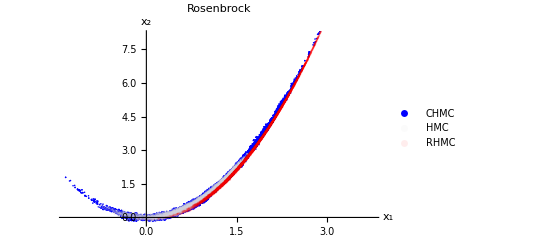

```mathematica
ListPlot[{QSchmc,QShmc,QSrhmc},PlotStyle->{Directive[Opacity[1],Blue],Directive[Opacity[.1],LightGray],Directive[Opacity[.07],Red]},PlotLegends->{Style["CHMC",Blue],Style["HMC",Gray],Style["RHMC",Red]},PlotLabel->Rosenbrock,AxesLabel->{"x_1","x_2"}]
```

10 chains trace

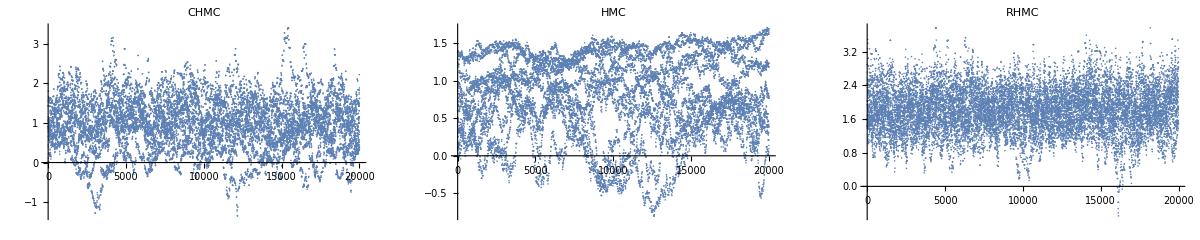

```mathematica
GraphicsRow[{ListPlot[QSchmc[[;;,1]],PlotLabel->"CHMC"],ListPlot[QShmc[[;;,1]],PlotLabel->"HMC"],ListPlot[QSrhmc[[;;,1]],PlotLabel->"RHMC"]}]
```